```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/y/Nutstore Files/1Project/0Expressivity/fisher/3code_paper/12RL_attention/RL_N3D10v4/TrainRew

```mathematica
DataRes = Import["rew_batch10.txt","Data"];
RewSet  = DataRes⟦All,2;;-1⟧;
Length[RewSet]
```

571

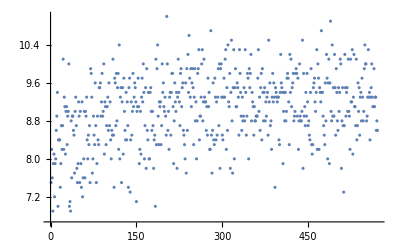

```mathematica
Score=Mean/@RewSet;
ListPlot[Score]
```

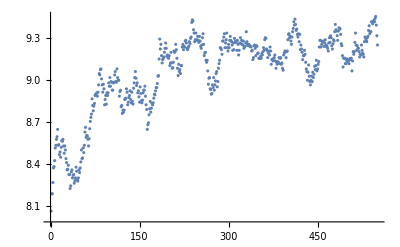

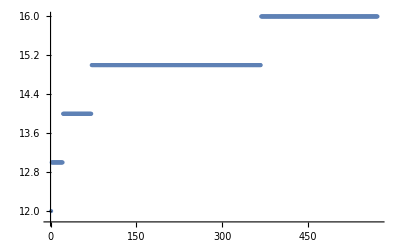

```mathematica
S= 20;
AvgScore=Table[Mean[Score⟦i;;i+S⟧],{i,1,Length[Score]-S}];
MaxRew=Table[Max[RewSet⟦1;;i,All⟧],{i,1,Length[Score]}];
ListPlot[AvgScore]
ListPlot[MaxRew,PlotRange->All]
```

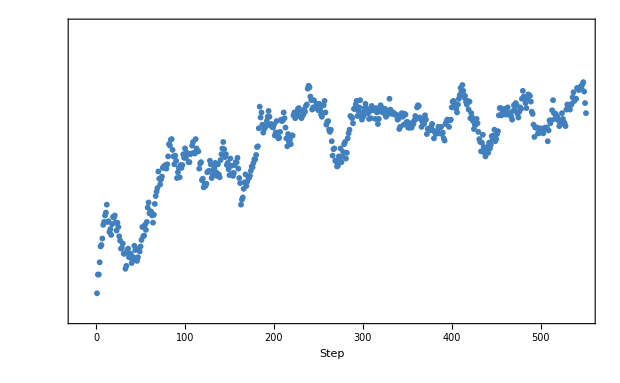
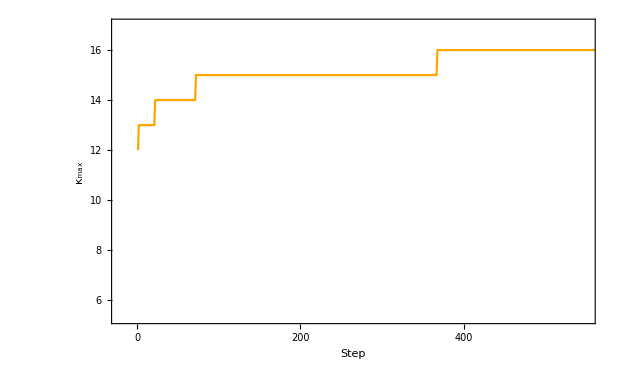

```mathematica
FigS=ListPlot[AvgScore,PlotRange->{{-20,550},{7.9,9.835}},PlotStyle->{RGBColor[0.25,0.5,0.75]},
PlotMarkers->{Style["•",FontSize->6]},
Frame->True,Axes->None,FrameStyle->Thick,FrameTicksStyle->Directive[Black,Bold,16],FrameTicks->{{None,{7,7.5,{8,"8.0"},8.5,{9,"9.0"},9.5,10}},{{0,100,200,300,400,500},None}},
FrameLabel->{{None,Style["Score^(———–)",Italic,Directive[Large],RGBColor[0.25,0.5,0.75],FontSize->20]},{Style["Step",Black,Directive[Large],FontSize->20],None}},RotateLabel->True,ImageSize->{620,350},ImagePadding->{{80,80},{60,10}}];
FigR=ListLinePlot[MaxRew,PlotRange->{{-20,550},{5.3,17}},PlotStyle->{RGBColor[1.0,0.647,0.0]},
(*PlotMarkers->{Style["•",FontSize->3]},*)
Frame->True,Axes->None,FrameStyle->Thick,FrameTicksStyle->Directive[Black,Bold,16],FrameTicks->{{{16,14,12,10,8,6},None},{{0,200,400,600,800,1000,1200},None}},
FrameLabel->{{Style["κ_max",Italic,Directive[Large],RGBColor[1.0,0.647,0.0],FontSize->20],None},{Style["Step",Black,Directive[Large],FontSize->20],None}},RotateLabel->True,ImageSize->{620,350},ImagePadding->{{80,80},{60,10}}];
Fig=Overlay[{FigS,FigR}]
```

```mathematica
Export["FigRLTrain.pdf",Fig]
```

FigRLTrain.pdf